```mathematica
n=7
b=2
a=-2
h=(b-a)/n
XDT={};YDT={};
For[i=0,i≤n,i++,
xdata[i]=a+i×h;
ydata[i]=N[Exp[-xdata[i]]+0.01*(-1)^(i+2)];
XDT=Append[XDT,xdata[i]];
YDT=Append[YDT,ydata[i]];];
Array[xdata,{n+1,0}];
Array[ydata,{n+1,0}];
MatrixForm[XDT]MatrixForm[YDT]
```

```mathematica
({{-2}, {-10/7}, {-6/7}, {-2/7}, {2/7}, {6/7}, {10/7}, {2}}) ({{7.39905609893065}, {4.162733883598096}, {2.3664184423836603}, {1.32071219744735}, {0.761477293075286}, {0.41437284567695}, {0.2496510364417758}, {0.1253352832366127}})
Array[difftab,{n+1,n+1},{0,0}];
For[k=1,k≤n,k++,
For[i=n,i≥n-k,i--,difftab[i,k]=""]];
For[i=0,i≤n,i++,difftab[i,0]=ydata[i]];
For [k=1, k≤n,k++,
For[i=0,i≤n-k,i++,
difftab[i,k]=(difftab[i+1,k-1]-difftab[i,k-1])/(xdata[i+k]-xdata[i])]];
tab1 = Array[difftab,{n+1,n+1}, {0,0}];
PaddedForm[TableForm[tab1],{6,5}]
```

{-14.7981,-5.94676,-2.02836,-0.377346,0.217565,0.355177,0.356644,0.250671}

7.39906 | -5.66356 |  2.20501 | -0.61579 |  0.16619 | -0.05956 |  0.02754 | -0.01298
 4.16273 | -3.14355 |  1.14937 | -0.23594 | -0.00399 |  0.03485 | -0.02440 | 
 2.36642 | -1.82999 |  0.74491 | -0.24505 |  0.09558 | -0.04880 |  | 
 1.32071 | -0.97866 |  0.32482 | -0.02657 | -0.04386 |  |  | 
 0.76148 | -0.60743 |  0.27927 | -0.12682 |  |  |  | 
 0.41437 | -0.28826 |  0.06187 |  |  |  |  | 
 0.24965 | -0.21755 |  |  |  |  |  | 
 0.12534 |  |  |  |  |  |  |

```mathematica
pln = difftab[0,0]+difftab[0,1]×(x-xdata[0]);
n=7;lst=List[pln];
For[k=2,k≤n,k++,
pln=lst[[k-1]]+difftab[0,k]×∏_(i=0)^(k-1) (x-xdata[i]);
lst=Append[lst,pln]];
nwtn[x_]:=N[lst[[n]]];
ColumnForm[lst]
```

7.39906-5.66356 (2+x)
7.39906-5.66356 (2+x)+2.20501 (10/7+x) (2+x)
7.39906-5.66356 (2+x)+2.20501 (10/7+x) (2+x)-0.61579 (6/7+x) (10/7+x) (2+x)
7.39906-5.66356 (2+x)+2.20501 (10/7+x) (2+x)-0.61579 (6/7+x) (10/7+x) (2+x)+0.166186 (2/7+x) (6/7+x) (10/7+x) (2+x)
7.39906-5.66356 (2+x)+2.20501 (10/7+x) (2+x)-0.61579 (6/7+x) (10/7+x) (2+x)+0.166186 (2/7+x) (6/7+x) (10/7+x) (2+x)-0.0595607 (-2/7+x) (2/7+x) (6/7+x) (10/7+x) (2+x)
7.39906-5.66356 (2+x)+2.20501 (10/7+x) (2+x)-0.61579 (6/7+x) (10/7+x) (2+x)+0.166186 (2/7+x) (6/7+x) (10/7+x) (2+x)-0.0595607 (-2/7+x) (2/7+x) (6/7+x) (10/7+x) (2+x)+0.0275364 (-6/7+x) (-2/7+x) (2/7+x) (6/7+x) (10/7+x) (2+x)
7.39906-5.66356 (2+x)+2.20501 (10/7+x) (2+x)-0.61579 (6/7+x) (10/7+x) (2+x)+0.166186 (2/7+x) (6/7+x) (10/7+x) (2+x)-0.0595607 (-2/7+x) (2/7+x) (6/7+x) (10/7+x) (2+x)+0.0275364 (-6/7+x) (-2/7+x) (2/7+x) (6/7+x) (10/7+x) (2+x)-0.0129839 (-10/7+x) (-6/7+x) (-2/7+x) (2/7+x) (6/7+x) (10/7+x) (2+x)

```mathematica
ColumnForm[Collect[lst,x]]
```

-3.92807-5.66356 x
2.37196+1.89647 x+2.20501 x^2
0.863901-1.6726 x-0.43409 x^2-0.61579 x^3
0.980183-0.99041 x+0.732606 x^2+0.143919 x^3+0.166186 x^4
0.99209-0.962229 x+0.60758 x^2-0.196428 x^3-0.089074 x^4-0.0595607 x^5
0.996808-0.956567 x+0.545007 x^2-0.273498 x^3-0.0328772 x^4+0.0348499 x^5+0.0275364 x^6
0.999987-0.954978 x+0.500188 x^2-0.295908 x^3+0.0413166 x^4+0.0719468 x^5+0.00156861 x^6-0.0129839 x^7

```mathematica
({{-2}, {-10/7}, {-6/7}, {-2/7}, {2/7}, {6/7}, {10/7}, {2}}) ({{7.39905609893065}, {4.162733883598096}, {2.3664184423836603}, {1.32071219744735}, {0.761477293075286}, {0.41437284567695}, {0.2496510364417758}, {0.1253352832366127}})
```

```mathematica
data = {{-2,7.39905609893065},{-10/7,4.162733883598096},{-6/7,2.3664184423836603},{-2/7,1.32071219744735},{2/7,0.761477293075286},{6/7,0.41437284567695},{10/7,0.2496510364417758},{2,0.1253352832366127}}
inpln:=InterpolatingPolynomial[data,x];
Collect[inpln,x]
```

{{-2,7.39906},{-10/7,4.16273},{-6/7,2.36642},{-2/7,1.32071},{2/7,0.761477},{6/7,0.414373},{10/7,0.249651},{2,0.125335}}

0.999987-0.954978 x+0.500188 x^2-0.295908 x^3+0.0413166 x^4+0.0719468 x^5+0.00156861 x^6-0.0129839 x^7

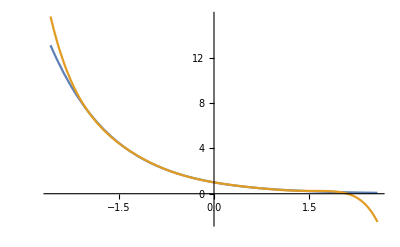

```mathematica
Plot[{Exp[-x],nwtn[x_]},{x,a-h,b+h}]
```

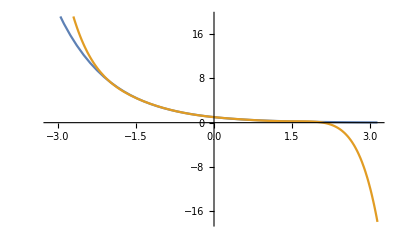

```mathematica
Plot[{Exp[-x],nwtn[x_]},{x,a-2h,b+2h}]
```

```mathematica
Pln={};P[n+1]=0;
For[i=n,i≥0,i--,P[i]=difftab[0,i]+(x-xdata[i])P[i+1];
Pln=Append[Pln,P[i]];]
ColumnForm[Pln]
```

-0.0129839
0.0275364-0.0129839 (-10/7+x)
-0.0595607+(0.0275364-0.0129839 (-10/7+x)) (-6/7+x)
0.166186+(-0.0595607+(0.0275364-0.0129839 (-10/7+x)) (-6/7+x)) (-2/7+x)
-0.61579+(0.166186+(-0.0595607+(0.0275364-0.0129839 (-10/7+x)) (-6/7+x)) (-2/7+x)) (2/7+x)
2.20501+(6/7+x) (-0.61579+(0.166186+(-0.0595607+(0.0275364-0.0129839 (-10/7+x)) (-6/7+x)) (-2/7+x)) (2/7+x))
-5.66356+(10/7+x) (2.20501+(6/7+x) (-0.61579+(0.166186+(-0.0595607+(0.0275364-0.0129839 (-10/7+x)) (-6/7+x)) (-2/7+x)) (2/7+x)))
7.39906+(2+x) (-5.66356+(10/7+x) (2.20501+(6/7+x) (-0.61579+(0.166186+(-0.0595607+(0.0275364-0.0129839 (-10/7+x)) (-6/7+x)) (-2/7+x)) (2/7+x))))

```mathematica
P[0]
```

7.39906+(2+x) (-5.66356+(10/7+x) (2.20501+(6/7+x) (-0.61579+(0.166186+(-0.0595607+(0.0275364-0.0129839 (-10/7+x)) (-6/7+x)) (-2/7+x)) (2/7+x))))

```mathematica
nwtn[x_]:=P[0];
m=70
XDAT={};YDAT={};nwtnDAT={};MR={};
For[i=0,i≤m,i++,
xdatas[i]=a+i×h/10;
ydatas[i]=N[Exp[-xdatas[i]]];
x=xdatas[i];
nwtndatas[i]=nwtn[i];
mr[i]=Abs[ydatas[i]-nwtndatas[i]];
XDAT=Append[XDAT,xdatas[i]];
YDAT=Append[YDAT, ydatas[i]];
nwtnDAT=Append[nwtnDAT,nwtndatas[i]];
MR=Append[MR,mr[i]];];
MatrixForm[N[XDAT]]MatrixForm[N[YDAT]]MatrixForm[N[nwtnDAT]]MatrixForm[MR]
```

70

(-2.
-1.94286
-1.88571
-1.82857
-1.77143
-1.71429
-1.65714
-1.6
-1.54286
-1.48571
-1.42857
-1.37143
-1.31429
-1.25714
-1.2
-1.14286
-1.08571
-1.02857
-0.971429
-0.914286
-0.857143
-0.8
-0.742857
-0.685714
-0.628571
-0.571429
-0.514286
-0.457143
-0.4
-0.342857
-0.285714
-0.228571
-0.171429
-0.114286
-0.0571429
0.
0.0571429
0.114286
0.171429
0.228571
0.285714
0.342857
0.4
0.457143
0.514286
0.571429
0.628571
0.685714
0.742857
0.8
0.857143
0.914286
0.971429
1.02857
1.08571
1.14286
1.2
1.25714
1.31429
1.37143
1.42857
1.48571
1.54286
1.6
1.65714
1.71429
1.77143
1.82857
1.88571
1.94286
2.) (0.01
0.0270188
0.049107
0.0598193
0.0621419
0.0585532
0.0510809
0.0413551
0.0306573
0.0199662
0.01
0.00125484
0.00595946
0.0114872
0.0152975
0.0174577
0.0181102
0.0174509
0.0157114
0.0131423
0.01
0.00653507
0.00298243
0.000446056
0.00356747
0.00623204
0.00832576
0.0097717
0.0105299
0.0105962
0.01
0.00880133
0.00708671
0.00496475
0.00256113
0.0000131033
0.00253614
0.00494334
0.00707095
0.0087929
0.01
0.010605
0.0105473
0.00979664
0.00835639
0.00626585
0.00360142
0.000476711
0.00295866
0.00652165
0.01
0.013158
0.015744
0.0175004
0.0181744
0.0175329
0.0153776
0.0115641
0.00602293
0.00121664
0.01
0.0200175
0.0307716
0.0415413
0.0513423
0.0588849
0.0625267
0.0602233
0.049474
0.0272634
0.01) (7.38906
6.97866
6.59106
6.22499
5.87925
5.55271
5.24431
4.95303
4.67794
4.41812
4.17273
3.94098
3.72209
3.51536
3.32012
3.13571
2.96155
2.79707
2.64172
2.49499
2.35642
2.22554
2.10193
1.98519
1.87493
1.77079
1.67244
1.57955
1.49182
1.40897
1.33071
1.2568
1.187
1.12107
1.05881
1.
0.944459
0.892003
0.84246
0.795669
0.751477
0.70974
0.67032
0.63309
0.597928
0.564718
0.533353
0.50373
0.475753
0.449329
0.424373
0.400803
0.378542
0.357517
0.337661
0.318907
0.301194
0.284466
0.268666
0.253744
0.239651
0.226341
0.213769
0.201897
0.190683
0.180092
0.17009
0.160643
0.151721
0.143294
0.135335) (7.39906
6.95164
6.54195
6.16517
5.8171
5.49415
5.19322
4.91168
4.64728
4.39815
4.16273
3.93972
3.72805
3.52685
3.33541
3.15317
2.97966
2.81452
2.65743
2.50813
2.36642
2.23208
2.10491
1.98474
1.87136
1.76456
1.66412
1.56978
1.48129
1.39837
1.32071
1.248
1.17991
1.11611
1.05625
0.999987
0.946995
0.896946
0.849531
0.804462
0.761477
0.720345
0.680867
0.642887
0.606284
0.570984
0.536955
0.504207
0.472794
0.442807
0.414373
0.387645
0.362798
0.340017
0.319486
0.301374
0.285817
0.272902
0.262643
0.254961
0.249651
0.246358
0.244541
0.243438
0.242025
0.238977
0.232617
0.220866
0.201195
0.170557
0.125335)

```mathematica
0.06252668312343929
```

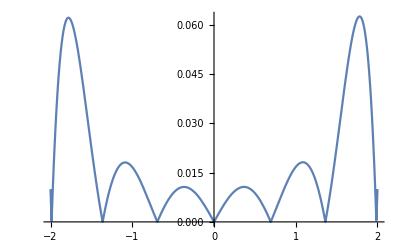

```mathematica
Plot[Abs[Exp[-x]-nwtn[x]],{x,-2,2}]
```

```mathematica
FindMaximum[{Abs[Exp[-x]-nwtn[x]],-2<x<-2},{x}]
```

{0.0622263,{2→-1.78092}}

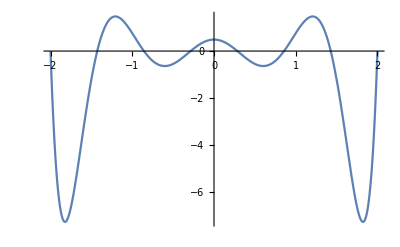

```mathematica
{0.062226345604599276,{2->-1.780918872571297}}
Plot[∏_(i=0)^n (x-xdata[i]),{x,-2,2}]
```

```mathematica
FindMaximum[{∏_(i=0)^n (x-xdata[i]),-2≤x≤-1},{x}]
```

```mathematica
{1.4749040152533832,{2->-1.2074687411948342}}



ⅇ^2/(8!)×1.4749040152533832
```

```mathematica
0.0002702913816777112
n1=8
b=2
a=-2
h=(b-a)/n1
XDT={};YDT={};
For[i=0,i≤n1,i++,
xdata1[i]=a+i×h;
ydata1[i]=N[Exp[-xdata1[i]]+0.01*(-1)^(i+2)];
XDT=Append[XDT,xdata1[i]];
YDT=Append[YDT,ydata1[i]];];
Array[xdata1,{n1+1,0}];
Array[ydata1,{n1+1,0}];
MatrixForm[XDT]MatrixForm[YDT]
```

```mathematica
({{-2}, {-3/2}, {-1}, {-1/2}, {0}, {1/2}, {1}, {3/2}, {2}}) ({{7.39905609893065}, {4.471689070338065}, {2.728281828459045}, {1.6387212707001282}, {1.01}, {0.5965306597126334}, {0.37787944117144234}, {0.2131301601484298}, {0.1453352832366127}})
Array[difftab,{n1+1,n1+1},{0,0}];
For[k=1,k≤n1,k++,
For[i=n1,i≥n1-k,i--,difftab[i,k]=""]];
For[i=0,i≤n1,i++,difftab[i,0]=ydata1[i]];
For [k=1, k≤n1,k++,
For[i=0,i≤n1-k,i++,
difftab[i,k]=(difftab[i+1,k-1]-difftab[i,k-1])/(xdata1[i+k]-xdata1[i])]];
tab1 = Array[difftab,{n+1,n1+1}, {0,0}];
PaddedForm[TableForm[tab1],{6,5}]
```

{-14.7981,-6.70753,-2.72828,-0.819361,0.,0.298265,0.377879,0.319695,0.290671}

7.39906 | -5.85473 |  2.36792 | -0.70682 |  0.22474 | -0.10392 |  0.05933 | -0.03278 |  0.01628
 4.47169 | -3.48681 |  1.30769 | -0.25734 | -0.03505 |  0.07406 | -0.05541 |  0.03234 | 
 2.72828 | -2.17912 |  0.92168 | -0.32745 |  0.15010 | -0.09217 |  0.05779 |  | 
 1.63872 | -1.25744 |  0.43050 | -0.02725 | -0.08032 |  0.08119 |  |  | 
 1.01000 | -0.82694 |  0.38964 | -0.18789 |  0.12265 |  |  |  | 
 0.59653 | -0.43730 |  0.10780 |  0.05740 |  |  |  |  | 
 0.37788 | -0.32950 |  0.19391 |  |  |  |  |  | 
 0.21313 | -0.13559 |  |  |  |  |  |  |

```mathematica
(f^(8)(ξ))/8!=0.01628
ξ=0.01628*8!
```

(f^8 ξ)/8≠0.01628

656.41

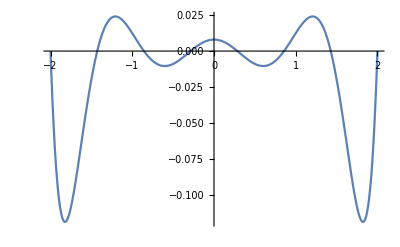

```mathematica
Plot[0.01628*∏_(i=0)^n (x-xdata[i]),{x,-2,2}]
```

```mathematica
FindMaximum[{0.01628*∏_(i=0)^n (x-xdata[i]),-2≤x≤2},{x}]
```

```mathematica
{0.02401143736832474,{2->1.207468692688361}}
```